## Strogatz Nonlinear Dynamics and Chaos Course

## Class 1

```mathematica
Solve[r x(1 - x/k)==0,x]
```

{{x→0},{x→k}}

```mathematica
D[r x(1 - x/k),x]//Simplify
```

r-(2 r x)/k

```mathematica
%212/.x->0
```

r

```mathematica
Unstable
```

```mathematica
%212/.x->k
```

-r

```mathematica
Stable
```

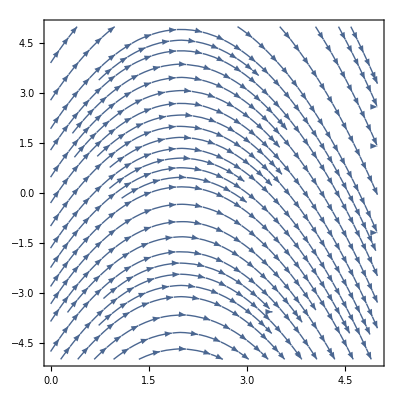

```mathematica
StreamPlot[{x,x 3(1-x/2)},{x,0,5},{y,-5,5}]
```

Exercise about the growth of a tumor

```mathematica
Solve[-a N Log[b N]==0,N]
```

{{N→1/b}}

```mathematica
N[t_]:=t
```

```mathematica
Plot[-N*Log[N],{N,1,100}]
```

Plot::plln: Limiting value 1 in {N,1,100} is not a machine-sized real number.

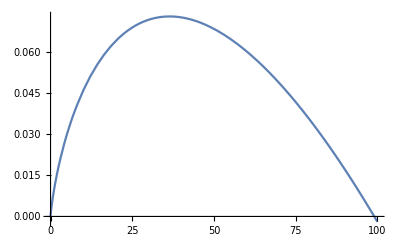

```mathematica
Plot[-.002*x*Log[.0101*x],{x,0,100}]
```

Saddle point bifurcation example - similar to the creation of critical points.  Saddle-node bifurcation occurs when tangent intersection happens:
∂_x (r+x)==∂_x (Log[1+x])

```mathematica
Manipulate[Plot[{Log[1+x],r+x/.r->3},{x,-5,5},PlotLabel->"Saddle Point Bifurcation Point"],{r,-3,5}]
```

See this creation and destruction of critical points for different values of r.  At r == 0 it is tangent to the curve so 1, r < 0 it intersects at two location, and finally if you make r > 0 there are no intersections.

```mathematica
Series[Log[1+x],{x,0,3}]
```

x-x^2/2+x^3/3+O[x]^4

Replace the log with a power series expansion

```mathematica
r+x-Log[1+x]/.{Log[1+x]->Series[Log[1+x],{x,0,2}]}
```

r+x^2/2+O[x]^3

Transcritical Bifurcation - critical points are stable when r < 0 and unstable when r > 0

```mathematica
f[x_]:=r x-x^2
```

```mathematica
Solve[f[x]==0,x]
```

{{x→0},{x→r}}

x = 0 is a fixed point ∀ r

```mathematica
fprime[x_]=D[f[x],x]
```

r-2 x

```mathematica
fprime[0]
```

r

```mathematica
fprime[r]
```

-r

Pitchfork bifurcation - occurs in systems with symmetry (left/right) below has x -> -x symmetry

```mathematica
f[x_]:=r x-x^3
```

```mathematica
Manipulate[Plot[{f[x]/.r->-1*n,f[x]/.r->0,f[x]/.r->n},{x,-10,10},PlotRange->All],{n,-25,25}]
```

```mathematica
Plot3D[r x-x^3,{r,-15,15},{x,-15,15}]
```

-Graphics3D-

```mathematica
Solve[f[x]==0,x]
```

{{x→0},{x→-√r},{x→√r}}

Bifurcation diagram of plotting the critical point curves - hence the supercritical pitchfork

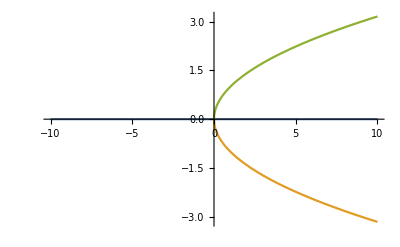

```mathematica
Plot[{0,-√r,√r},{r,-10,10}]
```

```mathematica
Solve[r-x^2==0,x]
```

{{x→-√r},{x→√r}}

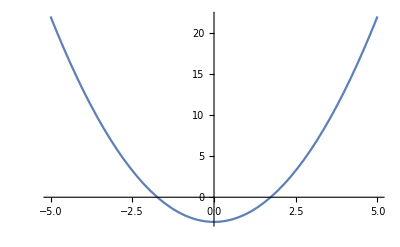

```mathematica
Plot[{r+x^2/.r->-3},{x,-5,5}]
```

### 3.6 Overdamped Bead on a Rotating Hoop

0, 1, and bifurcation of two roots based on gamma which is estimated as > 1, == 1, < 1

```mathematica
Solve[Cos[θ]==1/γ,θ]
```

{{θ→ConditionalExpression[-ArcCos[1/γ]+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[ArcCos[1/γ]+2 π C[1], C[1]∈ℤ]}}

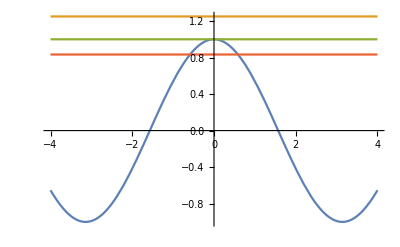

```mathematica
Plot[{Cos[θ],1/γ/.γ->0.8,1/γ/.γ->1,1/γ/.γ->1.2},{θ,-4,4}]
```

Solving for θ to plot the bifurcations that occur below were γ becomes a variable that is introduced for convenience

```mathematica
Solve[Cos[θ]==g/(r*ω^2)&&g>0&&0≤θ≤π&&r>0&&ω>0,θ]
```

{{θ→ConditionalExpression[ArcCos[g/(r ω^2)], g>0&&r>0&&ω>√(g/r)]}}

Stability not shown (need to figure out dashed line) the straight line from 1 becomes unstable at the bifurcation.  The other lines are stable.

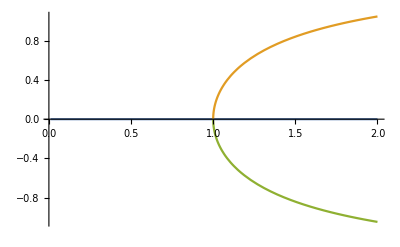

```mathematica
Plot[{ArcCos[1],ArcCos[1/γ],-ArcCos[1/γ]},{γ,0.01,2}]
```

Continuing the example of bead on a hoop that is spinning and finding its equilibrium points.  There is a linearization analysis that is done where you drop the ϕ'' time derivative.  It is motivated by showing that when you make things dimensionless that value is much smaller than the rest, so won' t have much effect in the limit. 

In that analysis you can then see the system though initially inaccurate since you dropped the second order term and can now no longer satisfy the initial conditions will still follow the trajectory in the long term (quickly move towards the curve + ϵ.

### 3.7 Insect Outbreak

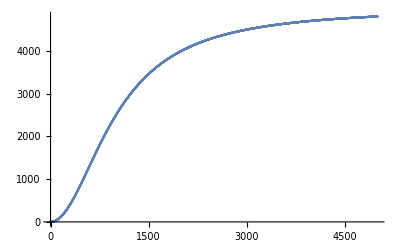

```mathematica
ListPlot[Table[(B*N^2)/(A^2+N^2)/.{B->5000,A->1000},{N,0,5000}]//N]
```

For dimensionless analysis you can apply the Buckingham pi theorem or just go after the idea that you want to get rid of units of time and population

```mathematica
xprime[x_,r_,k_]:=r x(1-x/k)-x^2/(1+x^2)
```

```mathematica
xprime[x,.48,10]
```

0.48 (1-x/10) x-x^2/(1+x^2)

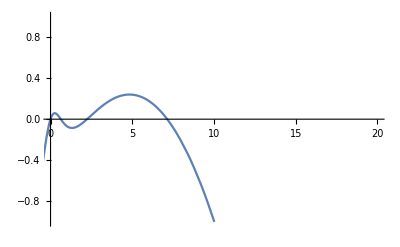

```mathematica
Plot[0.48 (1-x/10) x-x^2/(1+x^2),{x,-35.96456182726019,41.61765201652552},PlotRange->{{0,20},{-1,1}}]
```

```mathematica
Solve[xprime[x,r,k]==0,x]//First
```

{x→0}

Plot each side - r-(r x)/k becoming a line is why we scaled the eqn

```mathematica
Manipulate[Plot[{r-(r x)/k},{x,0,10}],{r,0,10},{k,1,10}]
```

```mathematica
Manipulate[Plot[{{x/(1+x^2),r-(r x)/k}},{x,0,80},PlotRange->{{0,20},{0,1}}],{r,0,0.5,0.1},{k,1,80}]
```

Zeroes are where these two (line and curve) intercept each other.  Up to 3 zeroes depending on the steepness of the line.

```mathematica
r (1-x/k)-x/(1+x^2)
```

r (1-x/k)-x/(1+x^2)

```mathematica
D[r (1-x/k),x]
```

-r/k

```mathematica
D[x/(1+x^2),x]
```

-(2 x^2)/((1+x^2)^2)+1/(1+x^2)

```mathematica
Simplify[-(2 x^2)/((1+x^2)^2)+1/(1+x^2)]
```

(1-x^2)/((1+x^2)^2)

```mathematica
(r-(r x)/k)/.{-r/k->(1-x^2)/((1+x^2)^2)}
```

r+(x (1-x^2))/((1+x^2)^2)

```mathematica
Simplify[r+(x (1-x^2))/((1+x^2)^2)]
```

```mathematica
Solve[r+(x-x^3)/((1+x^2)^2)==x/(1+x^2),r]
```

{{r→(2 x^3)/((1+x^2)^2)}}

```mathematica
-r/k==(1-x^2)/((1+x^2)^2)/.{r->(2 x^3)/((1+x^2)^2)}
```

```mathematica
Solve[-(2 x^3)/(k (1+x^2)^2)==(1-x^2)/((1+x^2)^2),k]
```

{{k→(2 x^3)/(-1+x^2)}}

```mathematica
r[x_]:=(2 x^3)/((1+x^2)^2)
```

```mathematica
k[x_]:=(2 x^3)/(-1+x^2)
```

```mathematica
Solve[k==k[x],x]
```

{{x→1/6 (k-k^2/((54 k-k^3+6 √3 √(27 k^2-k^4))^(1/3))-(54 k-k^3+6 √3 √(27 k^2-k^4))^(1/3))},{x→k/6+((1+ⅈ √3) k^2)/(12 (54 k-k^3+6 √3 √(27 k^2-k^4))^(1/3))+1/12 (1-ⅈ √3) (54 k-k^3+6 √3 √(27 k^2-k^4))^(1/3)},{x→k/6+((1-ⅈ √3) k^2)/(12 (54 k-k^3+6 √3 √(27 k^2-k^4))^(1/3))+1/12 (1+ⅈ √3) (54 k-k^3+6 √3 √(27 k^2-k^4))^(1/3)}}

Solve for x in terms of k and then substitute in to get r in terms of k.  Allows for plots of r as k varies.  The plot the positive solutions results in the bifurcation diagram.  Above region is one stable for the outbreak, middle region has bistable points, and below has one stable.  The curves are the tangential solutions so this they are the boundaries for when the critical points are created or annihilated.

```mathematica
sols=Solve[{k==k[x],r==r[x]},{x,r}];
```

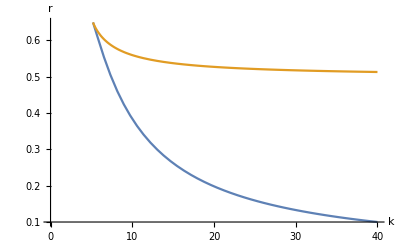

```mathematica
Plot[{r/.sols[[2]],r/.sols[[3]]},{k,0,40},AxesLabel->{"k","r"}]
```

See where these curves intersect and then plug in to the graph above to see where the intersect tangential

```mathematica
Solve[(r/.sols[[2]])==(r/.sols[[3]]),k]//N
```

{{k→5.19615}}

```mathematica
Re[r/.sols[[3]]/.k->5.19615//N]
```

0.649519

Example of getting other values for k and r where the curves intersect tangentially since they lay on the curves shown above

```mathematica
Table[Re[{k,r/.sols[[2]]}],{k,5,10}]//N
```

{{5.,0.662091},{6.,0.591095},{7.,0.524355},{8.,0.468597},{9.,0.422433},{10.,0.383971}}

```mathematica
xprime[x,r,k]
```

r x (1-x/k)-x^2/(1+x^2)

Catastrophe Cusp Surface - plotting the critical points on the r/k plane

```mathematica
ContourPlot3D[xprime[x,r,k]==0,{r,0
,1},{k,0,10},{x,0,10},BoxRatios->{1,0.6,0.4}]
```

### Flows on the Circle

Linear Stability analysis of the fixed points of thetaDot

```mathematica
thetaDot[ω_,a_,θ_]=ω-a Sin[θ]
```

ω-a Sin[θ]

```mathematica
D[thetaDot[1,1,n],n]
```

-Cos[n]

```mathematica
Solve[ω-a Sin[θ]==0,θ]
```

{{θ→ConditionalExpression[π-ArcSin[ω/a]+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[ArcSin[ω/a]+2 π C[1], C[1]∈ℤ]}}

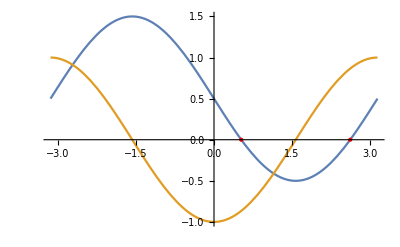

```mathematica
Plot[{thetaDot[1/2,1,n],-Cos[n]},{n,-π,π},Epilog->{Red, PointSize@Large, Point[{{π/6,0},{5 π/6,0}}]}]
```

Find the critical points - example is with actual numbers to see the stable critical point at 0.8

```mathematica
Solve[thetaDot[1/2,1,θ]==0,θ]
```

{{θ→ConditionalExpression[π/6+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[(5 π)/6+2 π C[1], C[1]∈ℤ]}}

```mathematica
-1 Cos[π/6+2 π]//N
```

-0.866025

```mathematica
Solve[thetaDot[ω,a,θ]==0,θ]
```

{{θ→ConditionalExpression[π-ArcSin[ω/a]+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[ArcSin[ω/a]+2 π C[1], C[1]∈ℤ]}}

Verify the critical points

```mathematica
thetaDot[a,ArcSin[ω/a]]
```

0

Linear stability analysis we take the derivative of our system and then plugin the critical points to check the slope

```mathematica
D[thetaDot[a,θ],θ]
```

-a Cos[θ]

```mathematica
-a Cos[θ]/.{θ->ArcSin[ω/a]}
```

-a √(1-ω^2/a^2)

```mathematica
-a Cos[θ]/.{θ->π-ArcSin[ω/a]+2 π}
```

a √(1-ω^2/a^2)

```mathematica
Integrate[1/thetaDot[ω,a,θ],{θ,0,2 π},Assumptions->a>0&&ω>0]
```

ConditionalExpression[(2 π)/(√(-a^2+ω^2)), a<ω]

Plot we can see at a = 0 T is equal to (2π)/ω as a uniform oscillator.  As a approach ω T blows up as seen below with a fixed ω of 1.

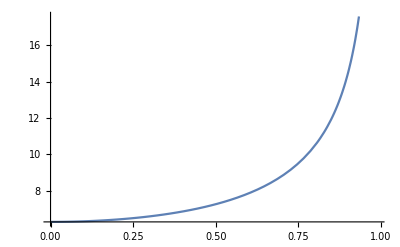

```mathematica
Plot[{(2 π)/(√(-a^2+ω^2))/.ω->1},{a,0,0.99}]
```

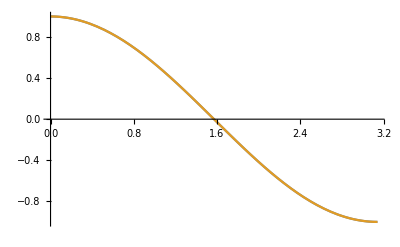

```mathematica
Plot[{Sin[θ+π/2],Cos[θ]},{θ,0,π}]
```

```mathematica
ω-Series[a Cos[θ],{θ,0,2}]
```

(-a+ω)+(a θ^2)/2+O[θ]^3

If we want the form x≂r+x^2 then

```mathematica
r+x^2/.{r->ω-a,x->√(a θ^2)/2}
```

-a+(a θ^2)/2+ω

```mathematica
Integrate[1/(r+x^2),{x,-∞,∞},Assumptions->r>0&&x>0]//Simplify
```

I’m not clear on the introduction of the √(2 θ^2)/a term

```mathematica
√(2 θ^2)/a π/(√r)/.{r->ω-a}
```

(√2 π √(θ^2/a))/(√(-a+ω))

Firefly synchronization

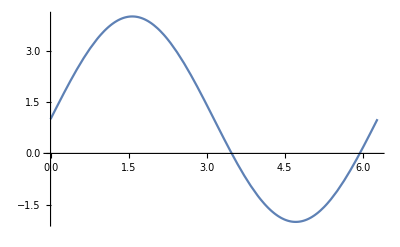

```mathematica
Plot[{ω+A Sin[d]/.{ω->1,A->3}},{d,0,2 π}]
```

Ω is Hz (per sec) and ω is Hz (per second) and A is the same units then one group is 
(Ω-ω)/A the other group is τ=A t (E/T*T == E).

Shows how the system is effected with a small μ vs large μ.  When μ is 0 phase difference is zero and the flashes are simultaneous. μ > 0 the phase difference is a constant (intercept on the x - axis > 0) phase locked.  Same frequency but not simultaneous.  Saddle point bifurcation occurs at μ = 1 which is no longer phase locked and drift increases.

```mathematica
Manipulate[Plot[{μ-Sin[ϕ]},{ϕ,-π,π},PlotLabel->"Modify the μ term to see the change in critical points"],{μ,-1,1,0.1}]
```

The range of entrainment

```mathematica
Solve[{(Ω-ω)/A==1},Ω]
```

{{Ω→A+ω}}

```mathematica
Solve[{(Ω-ω)/A==-1},Ω]
```

{{Ω→-A+ω}}

T_drift is for μ > 1 the time required to drift by 2 π

```mathematica
Integrate[1/(μ-A Sin[ϕ]),{ϕ,0,2 π},Assumptions->μ>0&&A>0]
```

```mathematica
ConditionalExpression[(2 π)/(√(-A^2+μ^2)), A<μ]/.{μ->Ω-ω}
```

ConditionalExpression[(2 π)/(√(-A^2+(-ω+Ω)^2)), A<-ω+Ω]

Exercises for 4

Must be 2 π periodic to have the vector field defined on the circle

```mathematica
Solve[Sin[a θ]==Sin[a (θ+2 π)],a]
```

{{a→ConditionalExpression[-2 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(-π/2+2 π C[1])/(π+θ), C[1]∈ℤ]},{a→ConditionalExpression[(π/2+2 π C[1])/(π+θ), C[1]∈ℤ]},{a→ConditionalExpression[-(π+2 π C[1])/π, C[1]∈ℤ]}}

The critical points are where Sin[2 θ] crosses the x - axis and this results in to stability alternating

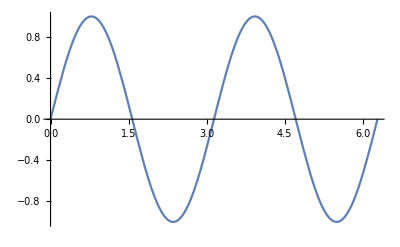

```mathematica
Plot[{Sin[2 θ]},{θ,0,2 π}]
```

```mathematica
Solve[Sin[2θ]==0 && 0≤θ≤2 π,θ]
```

{{θ→0},{θ→π/2},{θ→π},{θ→(3 π)/2},{θ→2 π}}

Exercise 4.2 .1

```mathematica
Solve[a*3==b*4,a,Integers]
```

{{a→ConditionalExpression[4 C[1], C[1]∈ℤ&&b==3 C[1]]}}

```mathematica
4*1*3==3*4
```

True

```mathematica
(1/3-1/4)^-1
```

12

Part 2 - Two - dimensional Systems

No chaos in ℝ^2, in ℝ^3 trajetories can intertwine and may lead to chaos (period 3)

Linear System
x' = A x where A is a matrix of constant coefficients

```mathematica
x[t_]=v ⅇ^(λ t);
```

```mathematica
D[x[t],t]
```

ⅇ^(t λ) v λ

Looking at solutions that go in a straight line

```mathematica
A x == A (x[t])
```

A x==A ⅇ^(t λ) v

```mathematica
DivideSides[ⅇ^(t λ) v λ==A x[t],ⅇ^(t λ),Assumptions->ⅇ^(t λ)>0]
```

v λ==A v

Above is the equation for eigenvalues and eigenvectors of A

```mathematica
Solve[λ^2-τ λ +Δ==0,λ]
```

{{λ→1/2 (τ-√(-4 Δ+τ^2))},{λ→1/2 (τ+√(-4 Δ+τ^2))}}

λ=∑eigenvalues (trace) and Δ=∏eigenvalues (determinant)

Saddle points mean determinant is negative Δ < 0, so λ_1>0&&λ_2<0,sotheeigenvaluesaredistinctandtheeigenvectorsarelinearlyindependent

https://youtu.be/QrHRaA93Nrg?t=2522

Attraction is a positive determinant Δ>0 and negative trace τ<0, repelling is positive determinant (Δ>0) and positive trace τ>0.

Nodes - τ^2+4Δ>0

Linear Systems on Love Affairs

```mathematica
A={{a,b},{b,a}}
```

{{a,b},{b,a}}

```mathematica
Eigensystem[A]
```

{{a-b,a+b},{{-1,1},{1,1}}}

```mathematica
Det[A]
```

a^2-b^2

```mathematica
Tr[A]
```

2 a

Example from the book 5.2.1

```mathematica
A={{1,1},{4,-2}}
```

{{1,1},{4,-2}}

```mathematica
Eigenvalues[A]
```

{-3,2}

```mathematica
Eigenvectors[A]
```

{{-1,4},{1,1}}

```mathematica
Solve[{2,-3}==c1{1,1}+c2 {1,-4},{c1,c2}]
```

{{c1→1,c2→1}}

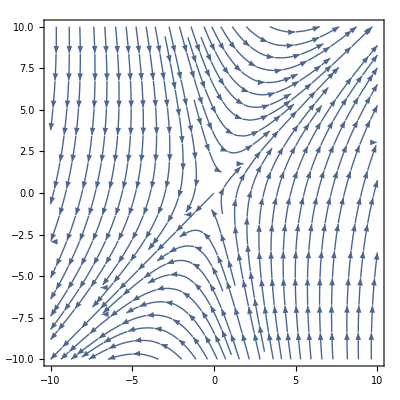

```mathematica
StreamPlot[{x+y,4 x-2 y},{x,-10,10},{y,-10,10}]
```

pplane phase portrait of the same system above

Complex λ and no real eigenvectors results in spirals in the phase portrait. λ=μ±ⅈω, where μ is the decay rate and ω is the speed of rotation

Classification of fixed points diagram at: with a plot of τ vs Δ plot which are results of the matrix A in that linear system.

https://youtu.be/QrHRaA93Nrg?t=4364

### Chapter 6 Two dimensional nonlinear systems

Approach to create Taylor series with two variable for linearizing the multi-dimensional system

```mathematica
Normal@Series[f[u,v]/.Thread[{u,v}->{u0,v0}+t {u-u0,v-v0}],{t,0,1}]/.t->1
```

f[u0,v0]+(v-v0) f^(0,1)[u0,v0]+(u-u0) f^(1,0)[u0,v0]

Drop the high order terms to linearize about the fixed points (saddle, node, or spiral) for this to work

```mathematica
Manipulate[StreamPlot[{-y+a x(x^2+y^2)/.a->1,x+a y(x^2+y^2)/.a->1},{x,-5,5},{y,-5,5},PlotLabel->"Change of the system wih a < 0,a == 0, and a > 0"],{a,-5,5}]
```

```mathematica
A={{-y,a x(x^2+y^2)},{x,a y(x^2+y^2)}}
```

{{-y,a x (x^2+y^2)},{x,a y (x^2+y^2)}}

```mathematica
xdot=-y+a x (x^2+y^2);
```

```mathematica
ydot=x+a y (x^2+y^2);
```

```mathematica
A.{1,1}
```

{-y+a x (x^2+y^2),x+a y (x^2+y^2)}

```mathematica
D[{xdot,ydot},{{x,y}}]/.{x->0,y->0}//MatrixForm
```

(0 | -1
1 | 0)

```mathematica
D[-y+a*x*x^2+a*x*y^2,{x}]/.{x->0,y->0}
```

0

6.4 Rabbits vs Sheep

```mathematica
Solve[{x (3-x-2y)==0,y (2-x-y)==0&&x≥0&&y≥0},{x,y}]
```

{{x→0,y→0},{x→0,y→2},{x→1,y→1},{x→3,y→0}}

The phase portrait that is created in the class by looking at the linearization of each critical point.  The math below shows what is seen in this portrait.

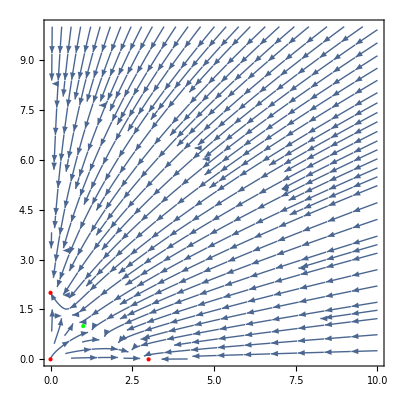

```mathematica
StreamPlot[{x (3-x-2y),y (2-x-y)},{x,0,10},{y,0,10},StreamPoints->Fine,Epilog->{{Red,Point[{0,0}]},{Red,Point[{0,2}]},{Green,Point[{1,1}]},{Red,Point[{3,0}]}}]
```

```mathematica
xdot=x (3-x-2y);
```

```mathematica
ydot=y (2-x-y);
```

Direct way of calculating the Jacobian

```mathematica
jacob=D[{xdot,ydot},{{x,y}}]
```

{{3-2 x-2 y,-2 x},{-y,2-x-2 y}}

```mathematica
jacob//MatrixForm
```

(3-2 x-2 y | -2 x
-y | 2-x-2 y)

```mathematica
Eigenvalues[jacob/.{x->0,y->0}]
```

{3,2}

```mathematica
Eigenvectors[jacob/.{x->0,y->0}]
```

{{1,0},{0,1}}

Both eigenvalues 3, 2 are positive so this is unstable node.  Trajectories leave along λ_2=2 since it is closer to 0 than λ_1.  Be in the eigendirection of {0,1}.

```mathematica
jacob/.{x->0,y->2}
```

(-1 | 0
-2 | -2)

Both eigenvalues are negative.  This is a stable node and the trajectories approach over λ_1 eigendirection which is {-1,2}.

```mathematica
Eigensystem[jacob/.{x->0,y->2}]
```

{{-2,-1},{{0,1},{-1,2}}}

```mathematica
Eigensystem[jacob/.{x->3,y->0}]
```

{{-3,-1},{{1,0},{-3,1}}}

Both eigenvalues are negative, so this is a stable node.  Trajectories approach λ_1 from the eigendirection of {-3, 1}

```mathematica
Eigensystem[jacob/.{x->1,y->1}]
```

{{-1-√2,-1+√2},{{√2,1},{-√2,1}}}

The negative determinant means this is a saddle pt and is unstable.

```mathematica
Det[jacob/.{x->1,y->1}]
```

-1

### Conservative Systems: no damping or external drive

(∂x)/(∂t)=F[x] is conservative if there is a "conserved quantity" for example energy E[x] that is constant on trajectors so its (∂E)/(∂t)=0

Example in class for a double well potential system (https : // youtu.be/3 s2lmZspEU8?t = 1348)

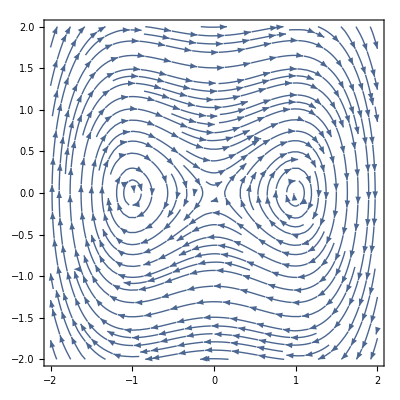

```mathematica
StreamPlot[{y,x-x^3},{x,-2,2},{y,-2,2},StreamPoints->Fine]
```

"homoclinic orbit" that starts and ends at the same fixed point.  Goes down the well picking up energy and then stopping at the top without rolling forward or back (interpreting this per the physics).

```mathematica
Plot3D[{1/2 y^2-1/2 x^2+1/4 x^4==0},{x,-2,2},{y,-2,2},PlotLabel->"Energy surface with z-axis being Energy"]
```

-Graphics3D-

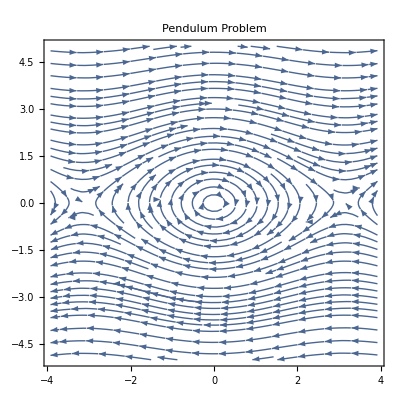

```mathematica
StreamPlot[{v,-Sin[θ]},{θ,-π-π/4,π+π/4},{v,-5,5},StreamPoints->Fine,PlotLabel->"Pendulum Problem"]
```

It has a heteroclinic orbit compared to a homoclinic orbit (one saddle point to another saddle point).  Interpret this as the pendulum swinging around based on whether its slowing down or speeding up, or going over the top based on the trajectories above.

## 6.8 Index Theory

Provides "global" information about the phase portrait of the system.

Definitions:

Simple closed curve (don’ t intersect itself).  A closed trajectory.  The curve does not pass through a fixed point.

Taking notes in rocket book, pdf in OneNote

Example of an Index value being greater than 1, for a complex vector field (dipole like)

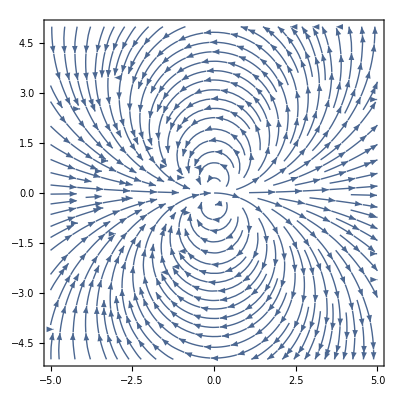

```mathematica
StreamPlot[{x^2-y^2,2 x y},{x,-5,5},{y,-5,5},StreamPoints->Fine]
```

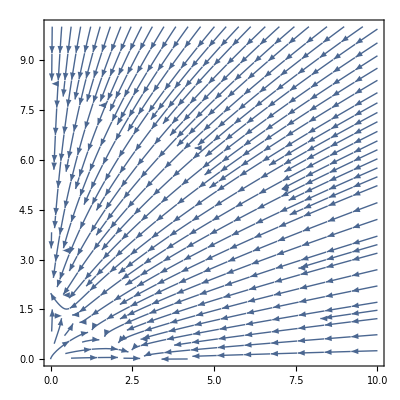

```mathematica
StreamPlot[{x(3-x-2y),y(2-x-y)},{x,0,10},{y,0,10},StreamPoints->Fine]
```

## Class 9: Testing for Closed Orbits

```mathematica
StreamPlot[{x(2-x-y),y(4x-x^2-3)},{x,0,5},{y,0,5},StreamPoints->Fine]
```

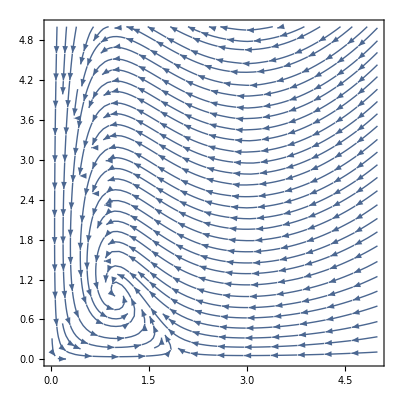

Dulac' s criterion for the existence of a closed orbit for the system above

```mathematica
g[x_,y_]:=1/(x y)
```

```mathematica
D[g[x,y]*x(2-x-y)//Simplify,x]
```

-1/y

```mathematica
Div[{g[x,y]*x(2-x-y),g[x,y]*y(4x-x^2-3)},{x,y}]
```

-1/y

Strictly negative in the region, so no closed orbits in this region

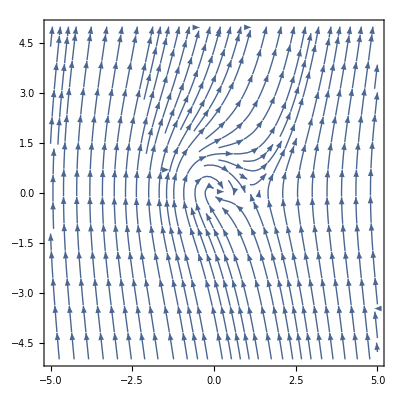

```mathematica
StreamPlot[{y,-x-y+x^2+y^2},{x,-5,5},{y,-5,5},StreamPoints->Fine]
```

```mathematica
g[x_]=ⅇ^(-2 x)
```

ⅇ^(-2 x)

```mathematica
Div[{g[x]*y,g[x]*(-x-y+x^2+y^2)},{x,y}]
```

-2 ⅇ^(-2 x) y+ⅇ^(-2 x) (-1+2 y)

```mathematica
Simplify[-2 ⅇ^(-2 x) y+ⅇ^(-2 x) (-1+2 y)]
```

-ⅇ^(-2 x)

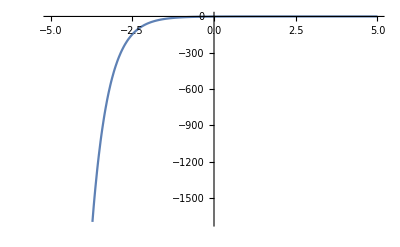

```mathematica
Plot[-ⅇ^(-2 x),{x,-5.,5}]
```

Calculated divergence above is always negative so no closed orbits

Simple example of creating a trapping region r_max and r_min

```mathematica
r(1-r^2)+μ r Cos[θ]//Factor
```

-r (-1+r^2-μ Cos[θ])

```mathematica
Reduce[r(1-r^2+μ)<0,r,Reals]
```

(μ≤-1&&r>0)||(μ>-1&&(-√(1+μ)<r<0||r>√(1+μ)))

```mathematica
r(1-r^2+μ)/.r->√(1+μ)//Simplify
```

0

Make sure you switch to polar coordinates if that is what you are using for the phase portrait.  You can see the limit cycle right in the center where field is unstable moving away and around that center the vector field is moving towards the center.

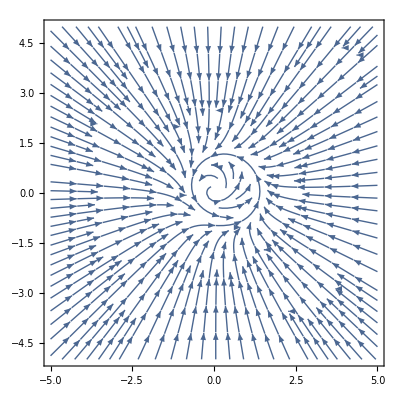

```mathematica
StreamPlot[Evaluate[TransformedField["Polar"->"Cartesian",{r(1-r^2)+μ r Cos[θ]/.μ->1,1},{r,θ}->{x,y}]],{x,-5,5},{y,-5,5},StreamPoints->Fine]
```

Example: Simple Glycolysis Model

Entering in the parameters for a, b based on the b/a plane that analyzed below.  With these values you now get a stable limit cycle and can see it in the phase portrait.

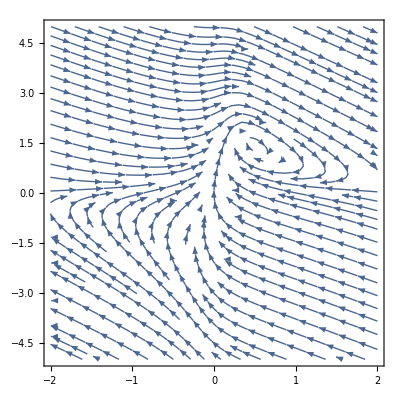

```mathematica
StreamPlot[{-x+a y+x^2 y,b-a y-x^2 y}/.{a->.1,b->.5},{x,-2,2},{y,-5,5},StreamPoints->Fine]
```

```mathematica
Solve[b-a y-x^2 y==0,y]
```

{{y→b/(a+x^2)}}

```mathematica
Solve[-x+a y+x^2 y==0,y]
```

{{y→x/(a+x^2)}}

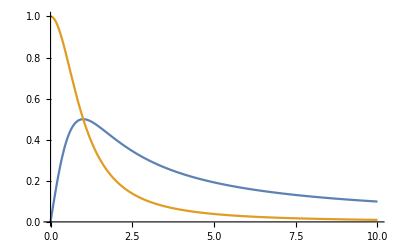

```mathematica
Plot[{x/(a+x^2)/.{a->1},b/(a+x^2)/.{a->1,b->1}},{x,0,10}]
```

Checking that the fixed point is a repellor

```mathematica
jacob=D[{-x+a y+x^2 y,b-a y-x^2 y},{{x,y}}]
```

```mathematica
{{-1+2 x y,a+x^2},{-2 x y,-a-x^2}}//MatrixForm
```

(-1+2 x y | a+x^2
-2 x y | -a-x^2)

Calculate the fixed point

```mathematica
Solve[{-x+a y+x^2 y==0,b-a y-x^2 y==0},{x,y}]
```

{{x→b,y→b/(a+b^2)}}

```mathematica
{{-1+2 x y,a+x^2},{-2 x y,-a-x^2}}/.{x->b,y->b/(a+b^2)}
```

{{-1+(2 b^2)/(a+b^2),a+b^2},{-(2 b^2)/(a+b^2),-a-b^2}}

```mathematica
Det[{{-1+(2 b^2)/(a+b^2),a+b^2},{-(2 b^2)/(a+b^2),-a-b^2}}]//FullSimplify
```

a+b^2

The determinant then is always positive as these were the kinetic parameters assumed to be > 0

```mathematica
Tr[{{-1+(2 b^2)/(a+b^2),a+b^2},{-(2 b^2)/(a+b^2),-a-b^2}}]//Simplify
```

-1-a+b^2 (-1+2/(a+b^2))

The trace is always negative

```mathematica
Plot3D[-1-a+b^2 (-1+2/(a+b^2)),{a,0,5.},{b,0,5}]
```

-Graphics3D-

```mathematica
Solve[-1-a+b^2 (-1+2/(a+b^2))==0,b]//Simplify
```

{{b→-(√(1-√(1-8 a)-2 a))/(√2)},{b→(√(1-√(1-8 a)-2 a))/(√2)},{b→-(√(1+√(1-8 a)-2 a))/(√2)},{b→(√(1+√(1-8 a)-2 a))/(√2)}}

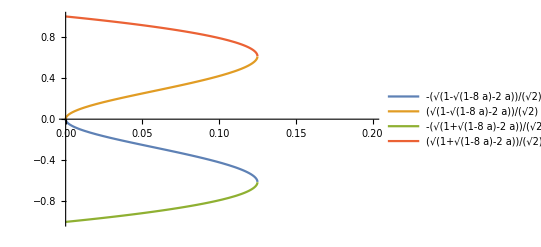

```mathematica
Plot[{-(√(1-√(1-8 a)-2 a))/(√2),(√(1-√(1-8 a)-2 a))/(√2),-(√(1+√(1-8 a)-2 a))/(√2),(√(1+√(1-8 a)-2 a))/(√2)},{a,0,.2},PlotLegends->"Expressions"]
```

This is the a/b parameter space.  The top portion is the unstable repellor, where the bottom is stable attractor.  Entering in a/b values in the original system where a/b are in the encompassed region by the curve will result in a phase portrait that has a stable limit cycle.

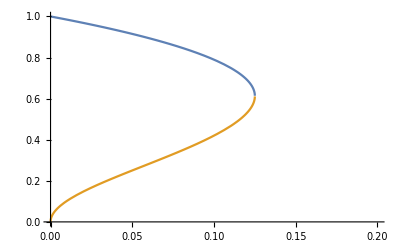

```mathematica
Plot[{(√(1+√(1-8 a)-2 a))/(√2),(√(1-√(1-8 a)-2 a))/(√2)},{a,0,.2}]
```

One way to find where it maximizes along the a axis (0.12 is mentioned in class).

```mathematica
Reduce[(√(1+√(1-8 a)-2 a))/(√2)>.2,a]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a≤0.125

Exercise 7.2 .10

```mathematica
Solve[{y-x^3==0,-x-y^3==0},{x,y}]
```

{{x→0,y→0},{x→-(-1)^(1/8),y→-(-1)^(3/8)},{x→(-1)^(1/8),y→(-1)^(3/8)},{x→-(-1)^(3/8),y→(-1)^(1/8)},{x→(-1)^(3/8),y→-(-1)^(1/8)},{x→-(-1)^(5/8),y→(-1)^(7/8)},{x→(-1)^(5/8),y→-(-1)^(7/8)},{x→-(-1)^(7/8),y→-(-1)^(5/8)},{x→(-1)^(7/8),y→(-1)^(5/8)}}

```mathematica
D[{a x[x]^2+b y[x]^2},{x}]
```

{2 a x[x] x'[x]+2 b y[x] y'[x]}

```mathematica
2 a x (y-x^3)+2 b y (-x-y^3)/.{b->a}
```

2 a x (-x^3+y)+2 a y (-x-y^3)

```mathematica
Simplify[2 a x (-x^3+y)+2 a y (-x-y^3)]
```

-2 a (x^4+y^4)

```mathematica
Manipulate[Plot3D[-2 a (x^4+y^4),{x,-0.3060086851928908,0.30601123951077147},{y,-0.30600866400064464,0.30601126070301765}],{a,1,5}]
```

Exercise 7.2.13

```mathematica
Ndot=Subscript[r, 1] Subscript[N, 1](1-Subscript[N, 1]/Subscript[K, 1])-Subscript[b, 1] Subscript[N, 1] Subscript[N, 2]
```

-b_1 N_1 N_2+N_1 (1-N_1/K_1) r_1

```mathematica
N2dot=Subscript[r, 2] Subscript[N, 2](1-Subscript[N, 2]/Subscript[K, 2])-Subscript[b, 2] Subscript[N, 1] Subscript[N, 2]
```

-b_2 N_1 N_2+N_2 (1-N_2/K_2) r_2

```mathematica
g=1/(Subscript[N, 1] Subscript[N, 2])
```

1/(N_1 N_2)

```mathematica
Div[{g*Ndot,g*N2dot},{Subscript[N, 1],Subscript[N, 2]}]//FullSimplify
```

-r_1/(K_1 N_2)-r_2/(K_2 N_1)

This is always less than 0 since all parameters were given as positive.

## Class 10 van der Pol Oscillator

7.5 μ >> 1 Relaxation oscillator

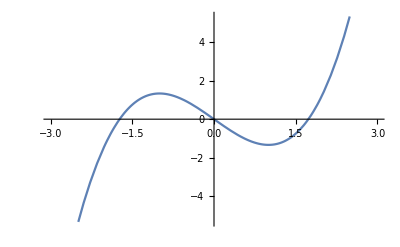

```mathematica
Plot[{μ (1/3 x^3-x)/.{μ->2}},{x,-3,3}]
```

Find the minimum value

```mathematica
FindMinimum[(1/3 x^3-x)&&x>0,x]
```

{-0.666667,{x→1.}}

Find the maximum value

```mathematica
FindMaximum[x^3/3-x,{x,-2}]
```

{0.666667,{x→-1.}}

Estimating the period after the substitutions to make it an integral in x

```mathematica
2* Integrate[-1/x μ(x^2-1),{x,2,1}]//Simplify
```

-μ (-3+Log[4])

Example of the van der Pol as weakly nonlinear so μ << 1

```mathematica
-ϵ*Integrate[A^2 Sin[t]^2(A^2 Cos[t]^2-1),{t,0,2π}]
```

-1/4 A^2 (-4+A^2) π ϵ

For this to be 0, A^2==4, so A=2.  This is the amplitude of the limit cycle

```mathematica
Cos[π/2]
```

0

7.6 Averaging Theory for weakly nonlinear oscillations

```mathematica
D[r[t]^2==x[t]^2+y[t]^2,t]//Simplify
```

r[t] r'[t]==x[t] x'[t]+y[t] y'[t]

```mathematica
D[t+ϕ[t]==ArcTan[(-y[t])/x[t]],t]//Simplify
```

1+ϕ'[t]==(y[t] x'[t]-x[t] y'[t])/(x[t]^2+y[t]^2)

```mathematica
Solve[1+ϕ'[t]==(y[t] x'[t]-x[t] y'[t])/(x[t]^2+y[t]^2),ϕ'[t]]//Simplify
```

{{ϕ'[t]→-(x[t]^2+y[t]^2-y[t] x'[t]+x[t] y'[t])/(x[t]^2+y[t]^2)}}

Keep trying the substitutions and simplifying

```mathematica
-(x[t]^2+y[t]^2-y[t] x'[t]+x[t] y'[t])/(x[t]^2+y[t]^2)/.{x[t]->r[t] Cos[t+ϕ[t]],y[t]->-r[t] Sin[t+ϕ[t]],x'[t]->y[t],y'[t]->-x[t]-ϵ h[x,y]}//Simplify
```

```mathematica
(ϵ Cos[t+ϕ[t]] h[x,y]-r[t]+Cos[t+ϕ[t]] x[t]-Sin[t+ϕ[t]] y[t])/r[t]/.{x[t]->r[t] Cos[t+ϕ[t]],y[t]->-r[t] Sin[t+ϕ[t]]}
```

(ϵ Cos[t+ϕ[t]] h[x,y]-r[t]+Cos[t+ϕ[t]]^2 r[t]+r[t] Sin[t+ϕ[t]]^2)/r[t]

```mathematica
Simplify[(ϵ Cos[t+ϕ[t]] h[x,y]-r[t]+Cos[t+ϕ[t]]^2 r[t]+r[t] Sin[t+ϕ[t]]^2)/r[t]]
```

(ϵ Cos[t+ϕ[t]] h[x,y])/r[t]

Plotting OverDot[r̄] from the example of the VDP oscillator

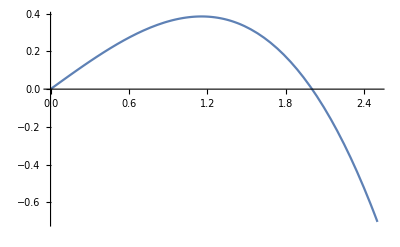

```mathematica
Plot[{r/8 (4-r^2)},{r,0,2.5}]
```

Solve the ODE?

```mathematica
Solve[{y==0,μ(1-x^2)y-x-a==0},{x,y}]
```

{{x→-a,y→0}}

Exercise 7.5.6 Biased van der Pol

2D Transformation system derived in pdf notes

Drawing the nullclines

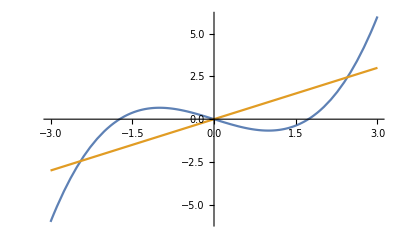

```mathematica
Plot[{a^3/3-a,a},{a,-3,3}]
```

```mathematica
F[x_]:=1/3 x^3-x
```

```mathematica
jacob=D[{μ(y-F[x]),1/μ(-x+a)},{{x,y}}]
```

{{(1-x^2) μ,μ},{-1/μ,0}}

```mathematica
jacob//MatrixForm
```

((1-x^2) μ | μ
-1/μ | 0)

```mathematica
jacob/.x->a
```

{{(1-a^2) μ,μ},{-1/μ,0}}

```mathematica
Eigensystem[jacob/.x->a]
```

{{(μ^2-a^2 μ^2-μ √(-4+μ^2-2 a^2 μ^2+a^4 μ^2))/(2 μ),(μ^2-a^2 μ^2+μ √(-4+μ^2-2 a^2 μ^2+a^4 μ^2))/(2 μ)},{{1/2 (-μ^2+a^2 μ^2+μ √(-4+μ^2-2 a^2 μ^2+a^4 μ^2)),1},{1/2 (-μ^2+a^2 μ^2-μ √(-4+μ^2-2 a^2 μ^2+a^4 μ^2)),1}}}

```mathematica
(μ^2-a^2 μ^2-μ √(-4+μ^2-2 a^2 μ^2+a^4 μ^2))/(2 μ)//Simplify
```

1/2 (μ-a^2 μ-√(-4+(-1+a^2)^2 μ^2))

```mathematica
jacob=D[{y,μ(1-x^2)y-x-a},{{x,y}}]
```

{{0,1},{-1-2 x y μ,(1-x^2) μ}}

```mathematica
Eigensystem[jacob]
```

{{1/2 (μ-x^2 μ-√(-4-8 x y μ+μ^2-2 x^2 μ^2+x^4 μ^2)),1/2 (μ-x^2 μ+√(-4-8 x y μ+μ^2-2 x^2 μ^2+x^4 μ^2))},{{-(-μ+x^2 μ-√(-4-8 x y μ+μ^2-2 x^2 μ^2+x^4 μ^2))/(2 (1+2 x y μ)),1},{-(-μ+x^2 μ+√(-4-8 x y μ+μ^2-2 x^2 μ^2+x^4 μ^2))/(2 (1+2 x y μ)),1}}}

Example for the Duffing equation

An explicit calculation of an average term (<>)_t notation in the class.  This is the change in phase that occurs from a spring that gets stiffer as it is pulled (ϵ>0)

```mathematica
ṙ==1/(2π) Integrate[Cos[s]^3,{s,0,2π}]
```

ṙ==0

```mathematica
ϕ̇==1/(2π) Integrate[Cos[s]^4,{s,0,2π}]
```

ϕ̇==3/8

Chapter 8 Bifurcations in 2 - D Systems

```mathematica
xdot=a-x^2
```

a-x^2

```mathematica
ydot=-y
```

-y

```mathematica
Manipulate[StreamPlot[{a-x^2,-y},{x,-5,5},{y,-5,5},StreamPoints->Fine,PlotLabel->"See the Bif'n happen as a approaches 0",Epilog->{{Red,Point[{Re[- √a],0}]},{Red,Point[{Re[√a],0}]}}],{a,-2,2}]
```

```mathematica
jacob=D[{a-x^2,-y},{{x,y}}]
```

{{-2 x,0},{0,-1}}

```mathematica
Eigensystem[jacob]//MatrixForm
```

(-1 | -2 x
{0,1} | {1,0})

```mathematica
Det[jacob]
```

2 x

```mathematica
Tr[jacob]
```

-1-2 x

```mathematica
Subscript[λ, 1]=-2 x
```

-2 x

```mathematica
Subscript[λ, 2]=-1
```

-1

```mathematica
Solve[{xdot==0 && a≥0,ydot==0},{x,y}]
```

{{x→ConditionalExpression[-√a, a>0],y→ConditionalExpression[0, a>0]},{x→ConditionalExpression[√a, a>0],y→ConditionalExpression[0, a>0]}}

If x is then a positive number λ_1 stays negative and this is a stable node.  This happens at fixed point x=√a,y=0.  The other point will be a saddle as λ_1 becomes negative when the fixed point is x=-√a.

Transcritical case - example not covered in class

```mathematica
xdot=a x-x^2;
```

```mathematica
ydot=-y;
```

```mathematica
critPts=Solve[{xdot==0,ydot==0},{x,y}]
```

{{x→0,y→0},{x→a,y→0}}

Can see the stability swap as a becomes positive

```mathematica
Manipulate[StreamPlot[{a x-x^2,-y},{x,-5,5},{y,-5,5},Epilog->{{Red,Point[{0,0}]},{Red,Point[{a,0}]}},StreamPoints->Fine,PlotLabel->"Transcritical Bif'n"],{a,-2,2}]
```

```mathematica
jacob=D[{a x-x^2,-y},{{x,y}}]
```

{{a-2 x,0},{0,-1}}

```mathematica
Eigensystem[jacob]//MatrixForm
```

(-1 | a-2 x
{0,1} | {1,0})

```mathematica
Det[jacob]
```

-a+2 x

```mathematica
Tr[jacob]
```

-1+a-2 x

Pitchfork (supercritical)

```mathematica
Solve[{a x-x^3==0,-y==0},{x,y}]
```

{{x→-√a,y→0},{x→√a,y→0},{x→0,y→0}}

You want to see this plot for a == 0, a < 0, and a > 0.  Watch the fixed points being created

```mathematica
Manipulate[StreamPlot[{a x-x^3,-y},{x,-5,5},{y,-5,5},StreamPoints->Fine,Epilog->{{Red,Point[{0,0}]},{Red,Point[{-Re[√a],0}]},{Red,Point[{
Re[√a],0}]}}],{a,-2,2}]
```

```mathematica
jacob=D[{a x-x^3,-y},{{x,y}}]
```

{{a-3 x^2,0},{0,-1}}

```mathematica
Eigensystem[jacob]//MatrixForm
```

(-1 | a-3 x^2
{0,1} | {1,0})

At origin (0,0) these eigenvalues would become:

```mathematica
Subscript[λ, 1]=-1
```

-1

```mathematica
Subscript[λ, 2]=a-3 x^2/.x->0
```

a

Hopf Bif' n

See a stable limit cycle when a > 0 below.  The limit cycle will appear as a becomes positive.

```mathematica
Manipulate[StreamPlot[Evaluate[TransformedField["Polar"->"Cartesian",{a r-r^3, w+b r^2/.{w->1,b->1}},{r,θ}->{x,y}]],{x,-5,5},{y,-5,5},StreamPoints->Fine,Epilog->{Red,If[a>0,Circle[{0,0},√a]]},StreamPoints->Fine],{a,-2,2}]
```

This is the circle of radius √a since we are in 2 D.

```mathematica
Solve[{a r-r^3==0},r]
```

{{r→0},{r→-√a},{r→√a}}

Get the Jacobian from the polar coordinate system.  Remember that the parameters are functions of t.

```mathematica
D[FromPolarCoordinates[{r[t],θ[t]}],t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]}

From notebook (derivation in pdf in OneNote)

```mathematica
jacob=D[{μ x-ω y,y μ+x ω},{{x,y}}]
```

{{μ,-ω},{ω,μ}}

```mathematica
jacob//MatrixForm
```

(μ | -ω
ω | μ)

We have eigenvalues that will cross the imaginary axis from left to right as μ increases

```mathematica
Eigensystem[jacob]
```

{{μ-ⅈ ω,μ+ⅈ ω},{{-ⅈ,1},{ⅈ,1}}}

Subcritical example

(8.4.1) Looking at the system as one dimensional and as a approaches the a_c

```mathematica
Manipulate[Plot[{a r+r^3-r^5},{r,0,1},AxesLabel->{r,ṙ}],{a,-.3,.3}]
```

```mathematica
Manipulate[StreamPlot[Evaluate[TransformedField["Polar"->"Cartesian",{a r+r^3-r^5,1},{r,θ}->{x,y}]],{x,-1,1},{y,-1,1},StreamPoints->Fine,Epilog->{{Red,If[-0.25≤a<0,Circle[{0,0},(√(1-√(1+4 a)))/(√2)]]},{Red,If[-0.25≤a<0||a>0,Circle[{0,0},(√(1+√(1+4 a)))/(√2)]]}}],{a,-0.5,0.5,0.01}]
```

```mathematica
Solve[{a r+r^3-r^5==0},r]
```

{{r→0},{r→-(√(1-√(1+4 a)))/(√2)},{r→(√(1-√(1+4 a)))/(√2)},{r→-(√(1+√(1+4 a)))/(√2)},{r→(√(1+√(1+4 a)))/(√2)}}

```mathematica
Table[{-(√(1-√(1+4 a)))/(√2),(√(1-√(1+4 a)))/(√2),-(√(1+√(1+4 a)))/(√2),(√(1+√(1+4 a)))/(√2)},{a,-0.25,0.25,.1}]
```

{{-0.707107,0.707107,-0.707107,0.707107},{-0.428687,0.428687,-0.903453,0.903453},{-0.229753,0.229753,-0.973249,0.973249},{0.-0.218455 ⅈ,0.+0.218455 ⅈ,-1.02358,1.02358},{0.-0.363944 ⅈ,0.+0.363944 ⅈ,-1.06417,1.06417},{0.-0.45509 ⅈ,0.+0.45509 ⅈ,-1.09868,1.09868}}

This would the values of a that ensure the numerator is real

```mathematica
Reduce[√(1+4 a)<1,a]
```

-1/4≤a<0

Nullclines

```mathematica
Solve[{a-x-(4x y)/(1+x^2)==0},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→((a-x) (1+x^2))/(4 x)}}

```mathematica
Solve[{b x(1-y/(1+x^2))==0},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0},{y→1+x^2}}

8.1.6 exercise

```mathematica
Solve[{y-2x==0},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→2 x}}

```mathematica
Solve[{μ+x^2-y==0},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→x^2+μ}}

```mathematica
Manipulate[Plot[{2x,x^2+μ},{x,-5,5}],{μ,-2,2}]
```

```mathematica
Solve[{-2x+x^2+μ==0},x]
```

{{x→1-√(1-μ)},{x→1+√(1-μ)}}

```mathematica
jacob=D[{y-2x,μ+x^2-y},{{x,y}}]
```

{{-2,1},{2 x,-1}}

```mathematica
Det[jacob]
```

2-2 x

```mathematica
Tr[jacob]
```

-3

```mathematica
Eigensystem[jacob]
```

{{1/2 (-3-√(1+8 x)),1/2 (-3+√(1+8 x))},{{-(1+√(1+8 x))/(4 x),1},{-(1-√(1+8 x))/(4 x),1}}}

Determining when the eigenvalues have no imaginary component

```mathematica
Reduce[Sqrt[1+8 x]==0,x]
```

x==-1/8

```mathematica
Reduce[1/2 (-3-√(1+8 x))<0&&1/2 (-3+√(1+8 x))<0,x]
```

-1/8≤x<1

```mathematica
1/2 (-3-√(1+8 x))/.x->-1/8//N
```

-1.5

```mathematica
Manipulate[StreamPlot[{y-2x,μ+x^2-y},{x,-5,5},{y,-5,5},StreamPoints->Fine,Epilog->{{Red,Point[{1-√(1-μ),2 (1-√(1-μ))}]},{Red,Point[{1+√(1-μ),2 (1+√(1-μ))}]}}],{μ,-.27,1}]
```

At the origin then the point would be a stable spiral when μ<-1/8, since the eigenvalues are complex and the real part is negative.  Stable node at -1/8≤x<1 since both eigenvalues are real and negative.

## 8.4 other bif' n of periodic orbits

SNIPER - saddle - node bifurcation of cycles

```mathematica
Manipulate[StreamPlot[Evaluate[TransformedField["Polar"->"Cartesian",{r(1-r^2),ω-Sin[θ]},{r,θ}->{x,y}]],{x,-2,2},{y,-2,2},StreamPoints->Fine,PlotLabel->"3 cases to look at ω=1, ω<1, and ω>1"],{ω,-1.5,1.5}]
```

```mathematica
Manipulate[Plot[{a r+r^3-r^5},{r,0,1}],{a,-.3,.3}]
```

```mathematica
Integrate[1/(ω-Sin[θ]),{θ,0,2 π},Assumptions->ω>0]
```

ConditionalExpression[(2 π)/(√(-1+ω^2)), ω>1]

```mathematica
Limit[  Sqrt[1+ω],ω->1]
```

√2

```mathematica
Manipulate[Plot[{ω-Sin[θ]},{θ,0,2 π},PlotLabel->"Seeing what happens when ω goes to 1"],{ω,0,1}]
```

## Class 14: 8.6 Coupled Oscillators and Quasiperiodicity

```mathematica
KnotData["Trefoil"]
```

-Graphics3D-

```mathematica
Table[{Mod[x,2 π],Mod[y,2 π]},{x,0,6 π},{y,0,6 π}];
```

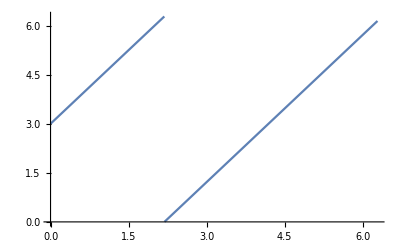

```mathematica
Plot[{Mod[3/2 Mod[x,2 π] + 3,2 π]},{x,0,2 π}]
```

```mathematica
Clear[tmax,ω1,ω2]
ω1=ⅇ; (*ω natural frequency*)
ω2=1;
tmax=3 π;
```

```mathematica
dθ1=ω1; (*θ phase*)
dθ2=ω2;
sp=StreamPlot[{dθ1,dθ2},{θ1,0,2 π},{θ2,0,2 π},FrameLabel->{Subscript[θ, 1][t],Subscript[θ, 2][t]},LabelStyle->20];
```

```mathematica
integ=NDSolve[{
θ1'[t]==ω1,
θ2'[t]==ω2,
θ1[0]==0,θ2[0]==1},
{θ1,θ2},{t,0,tmax}];
plot1=ParametricPlot[Evaluate[{θ1[t],θ2[t]}/.integ],{t,0,tmax},AxesLabel->{Subscript[θ, 1][t],Subscript[θ, 2][t]},ImageSize->260,PlotStyle->Red,LabelStyle->20];
```

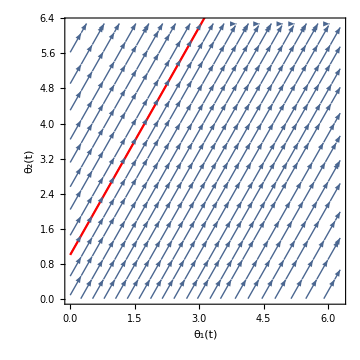

```mathematica
Show[sp,plot1]
```

See the other notebooks with Torus trajectory animations showing the dense orbits and knots

## Class 15 Chaotic Waterwheel

```mathematica
Integrate[D[m[θ],θ],{θ,Subscript[θ, 1],Subscript[θ, 2]}]//Simplify
```

∫_θ_1^θ_2 m'[θ]ⅆθ

FTC argument during the derivation of the mass and partial w.r.t t

```mathematica
-Integrate[D[Sin[x],x],{x,π/2,π}]
```

1

```mathematica
Sin[π/2]-Sin[0]
```

1

Gravity or g_effective based on the tilt of the wheel

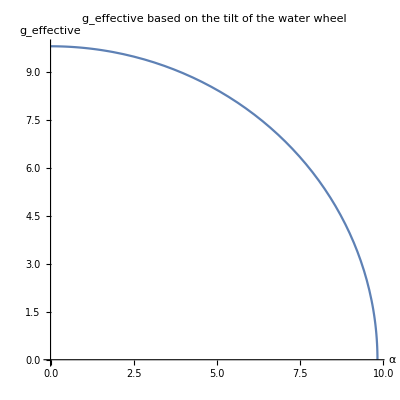

```mathematica
ParametricPlot[{9.82 Cos[α],9.82 Sin[α]},{α,0,π/2},AxesLabel->{"α","g_effective"},PlotLabel->"g_effective based on the tilt of the water wheel"]
```

This represents the side view of the wheel, so when laying flat it has no tendency to turn so the g_effective would just be 0.  When elevated π/2 radians, then you'd have all of gravity turning the wheel, like on a car.

The argument for the interital term becoming a constant as t → ∞ which in practice would be closer to being >> 1/K is below.  The value of m[t] would then be Q/K.  Mass in the wheel goes to the constant of inflow/(outflow (drainage)).

```mathematica
Limit[m[t]/.DSolve[{m'[t]==Q-K m[t]},m[t],t],t->∞,Assumptions->Q∈Reals&&Q>0&&K>0]
```

{Q/K}

This motivates then being able to treat I (inertia) as a constant and not dependent on t

Get coefficient of the Sin[n θ] term from the partial w.r.t t

```mathematica
D[Subscript[a, n][t] Sin[n θ],t]
```

Sin[n θ] a_n'[t]

```mathematica
D[Subscript[a, n][t] Sin[n θ]+Subscript[b, n][t] Cos[n θ],θ]
```

n Cos[n θ] a_n[t]-n Sin[n θ] b_n[t]

Refresh of orthogonal functions ∫f(x) g(x) dx == 0, for this case Cos[x] and Sin[x]

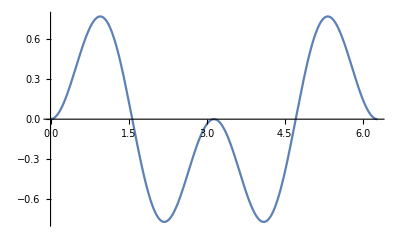

```mathematica
Plot[{Sin[θ]*Sin[2 θ]},{θ,0,2 π}]
```

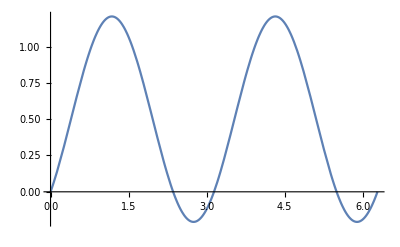

```mathematica
Plot[{Sin[θ]^2+( Sin[θ] Cos[θ])},{θ,0,2 π}]
```

```mathematica
Integrate[Sin[θ]^2,{θ,0,2 π}]==Integrate[(Sin[θ]+Cos[θ]) Sin[θ],{θ,0,2 π}]
```

True

```mathematica
Sum[(Subscript[a, n] Sin[n θ]+Subscript[b, n] Cos[n θ]) Sin[θ],{n,0,2}]//Expand
```

Sin[θ]^2 a_1+Sin[θ] Sin[2 θ] a_2+Sin[θ] b_0+Cos[θ] Sin[θ] b_1+Cos[2 θ] Sin[θ] b_2

```mathematica
Integrate[Sin[θ](Sin[2 θ]),{θ,0,2 π}]
```

0

```mathematica
Integrate[Sum[(Subscript[a, n] Sin[n θ]+Subscript[b, n] Cos[n θ]) Sin[θ],{n,0,5}],{θ,0,2 π}]
```

π a_1

Class 16 Waterwheel equations and Lorenz Equations (6/22/2020)

```mathematica
Solve[{Subscript[a, 1]==(Subscript[q, 1]-K Subscript[b, 1])/ω/.Subscript[a, 1]->(Subscript[b, 1] ω)/K},Subscript[b, 1]]
```

{{b_1→(K q_1)/(K^2+ω^2)}}

Class 16 System is dissipative, in that volumes in the phase space contract under flow derivation (56:38)

```mathematica
Div[{σ (y-x),r x-y-x z,x y-b z},{x,y,z}]
```

-1-b-σ

This is all negative (-(1 - b - σ) < 0) so will always be < 0 given the parameters are positive.  This is a constant

```mathematica
DSolve[{v'[t]==-(σ+b+1)v[t],v[0]==V}, v[t],t]
```

{{v[t]→ⅇ^(-t-b t-t σ) V}}

Fixed points for the Lorenz equations (includes C^* and C^-

```mathematica
Solve[{σ (y-x)==0,r x-y-x z==0,x y-b z==0},{x,y,z}]
```

{{x→0,y→0,z→0},{x→-√b √(-1+r),y→-√b √(-1+r),z→-1+r},{x→√b √(-1+r),y→√b √(-1+r),z→-1+r}}

```mathematica
jacob=D[{σ(y-x),r x-y},{{x,y}}]
```

{{-σ,σ},{r,-1}}

```mathematica
Tr[jacob]
```

-1-σ

```mathematica
Det[jacob]
```

σ-r σ

Exercise 9.2.1Stability of C^*and C^-

Set up the matrix for the system of equations by terms x,y,z

```mathematica
{Collect[{σ (y-x)==0,r x-y-x z==0,x y-b z==0},{x}],Collect[{σ (y-x)==0,r x-y-x z==0,x y-b z==0},{y}],
Collect[{σ (y-x)==0,r x-y-x z==0,x y-b z==0},{z}]}
```

{{-x σ+y σ==0,-y+x (r-z)==0,x y-b z==0},{-x σ+y σ==0,r x-y-x z==0,x y-b z==0},{(-x+y) σ==0,r x-y-x z==0,x y-b z==0}}

```mathematica
m={{-σ,σ,0},{(r-z),-1,x},{y,x,-b }}
```

{{-σ,σ,0},{r-z,-1,x},{y,x,-b}}

```mathematica
MatrixForm[m]
```

(-σ | σ | 0
r-z | -1 | x
y | x | -b)

Another approach is to just generate the Jacobian directly

```mathematica
jacob=D[{σ (y-x),r x-y-x z,x y-b z},{{x,y,z}}]
```

{{-σ,σ,0},{r-z,-1,-x},{y,x,-b}}

```mathematica
MatrixForm[jacob]
```

(-σ | σ | 0
r-z | -1 | -x
y | x | -b)

```mathematica
MatrixForm[jacob/.{x->-√b √(-1+r),y->-√b √(-1+r),z->-1+r}]
```

(-σ | σ | 0
1 | -1 | √b √(-1+r)
-√b √(-1+r) | -√b √(-1+r) | -b)

Exercise 9.2.3 Sketch

```mathematica
V=x^2+y^2+(z-r-σ)^2
```

x^2+y^2+(-r+z-σ)^2

```mathematica
D[x[t]^2+y[t]^2+(z[t]-r-σ)^2==C[t],{t}]
```

2 x[t] x'[t]+2 y[t] y'[t]+2 (-r-σ+z[t]) z'[t]==C'[t]

```mathematica
1/2 (2 x[t] x'[t]+2 y[t] y'[t]+2 (-r-σ+z[t]) z'[t])/.{x'[t]->σ (y[t]-x[t]),y'[t]->r x[t]-y[t]-x[t] z[t],z'[t]->x[t] y[t]-b z[t]}//Simplify
```

-σ x[t]^2-y[t]^2+b (r+σ-z[t]) z[t]

```mathematica
Expand[-σ x[t]^2-y[t]^2+b (r+σ-z[t]) z[t]]
```

-σ x[t]^2-y[t]^2+b r z[t]+b σ z[t]-b z[t]^2

```mathematica
-σ x[t]^2-y[t]^2+b r z[t]+b σ z[t]-b z[t]^2/.{b->8/3,r->28,σ->10}
```

-10 x[t]^2-y[t]^2+(304 z[t])/3-(8 z[t]^2)/3

```mathematica
Solve[15==-z(10+80/3),z]
```

{{z→-9/22}}

```mathematica
ContourPlot3D[{-10 x^2-y^2-8/3 z^2==-z (304/3)},{x,-30,30},{y,-30,30},{z,-10,50},AxesLabel->Automatic,PlotLabel->"Ellipsoid with Lorenz Constants (r=28)"]
```

-Graphics3D-

```mathematica
ContourPlot3D[{-10 x^2-y^2-80/3 z^2==-z (10 +80/3)(*,x^2+y^2+z^2==10*)},{x,-5,5},{y,-5,5},{z,-5,5},AxesLabel->Automatic,PlotLabel->"Ellipsoid with Lorenz Constants w/ r=1"]
```

-Graphics3D-

```mathematica
If-∇F*x̄'>0, all flow is inward alternative derivation
```

```mathematica
Div[{x^2,y^2,(z-r-σ)^2},{x,y,z}]
```

2 x+2 y+2 (-r+z-σ)

Is this a node or spiral?

```mathematica
Tr[jacob]^2-4 Det[jacob]
```

(-1-σ)^2-4 (σ-r σ)

```mathematica
Simplify[(-1-σ)^2-4 (σ-r σ)]
```

1+(-2+4 r) σ+σ^2

```mathematica
Reduce[%266>0,r]
```

r∈ℝ&&((σ<0&&r<(-1+2 σ-σ^2)/(4 σ))||σ==0||(σ>0&&r>(-1+2 σ-σ^2)/(4 σ)))

Playing around drawing a phase portrait using the parameter values from Lorenz' s paper and then changing r

```mathematica
Manipulate[VectorPlot3D[{Evaluate[σ (y-x)/.σ->10],Evaluate[r x-y-x z],Evaluate[x y-b z/.b->8/3]},{x,-10,10},{y,-10,10},{z,-10,10},VectorPoints->Fine,VectorSizes->0.5,VectorMarkers->"Arrow",ImageSize->Large],{r,-5,5,1}]
```

When r < 1 (Rayleigh number) all trajectories go to origin.  Proof using Liaponuv functions

```mathematica
Reduce[(r+1)x y-x^2-y^2-b z^2<0&&r<1&&b>0&&x!=0&&y!=0&&z!=0,r]//Simplify
```

b>0&&z≠0&&(((x^2-x y+y^2+b z^2)/(x y)<r<1&&((y>0&&x<0)||(x>0&&y<0)))||(r<1&&((x<0&&y<0)||(x>0&&y>0))))

```mathematica
jacob=D[{σ(y-x),r x-y,-bz},{{x,y}}]
```

{{-σ,σ},{r,-1},{0,0}}

Liapunov Time (predictability in a chaotic system) where λ is Liapunov exponent

```mathematica
Solve[Subscript[δ, 0] ⅇ^(λ t)==a,t,Reals]
```

{{t→ConditionalExpression[Log[a/δ_0]/λ, (a>0&&δ_0>0)||(a<0&&δ_0<0)]}}

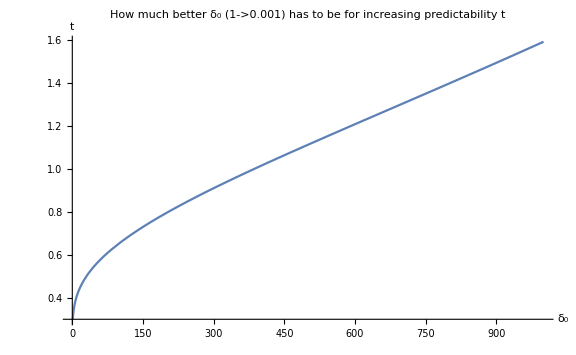

```mathematica
Plot[{1/0.9 Log[5000 1/Subscript[δ, 0],10]},{Subscript[δ, 0],1,1000},AxesLabel->{Subscript[δ, 0],t},PlotLabel->"How much better δ_0 (1->0.001) has to be for increasing predictability t",ImageSize->Large]
```

## Class 19 1-D Maps - 7/1/2020

### Orbit Diagram from Robert May

### Original approach doesn’t' t let r go past 3

```mathematica
f[r_][x_]:=r(1-x);
```

```mathematica
cps[r_]=x/.Quiet[Solve[D[f[r][x],x]==0,x]]
```

x

```mathematica
criticalOrbits[r_,cp_]:=Module[{try},If[Head[cp]===Real,try=NestWhileList[f[r],cp,Abs[#]<100&,1,1000];
If[Abs[Last[try]]≥100,try={},try=Drop[{a,#}&/@try,10]],{}]];
```

```mathematica
points[k_]:=Partition[Flatten[Table[criticalOrbits[r,cps[r][[k]]],{r,0.5,3.86,0.001}]],2]
```

```mathematica
Quiet[Rasterize[Graphics[{Opacity[0.02],PointSize[0.002],Table[{ColorData[1,k],Point[points[k]]},{k,1,Length[cps[r]]}]},Frame->True]]]
```

### Based off the Chaos in three lines from Strogatz' s twitter account (change syntax around on the function definition and NestList

```mathematica
f[r_][x_]:=r x(1-x); (*r Sin[π x];*)
```

```mathematica
Flatten[ParallelTable[{r,#}&/@Take[NestList[f[r][#]&,Exp[-1],2000],-1000],{r,3.44,4,0.0005}],1];
```

```mathematica
ListPlot[%64]
```

-Graphics-

```mathematica
Rasterize[ListPlot[%,PlotStyle->Directive[PointSize@0,Opacity@0.1],ImageSize->Full]]
```

-Graphics-

Calculuate p and q points for r > 3.  Apply the map (compositoin) divide the trivial solutions out (x and 1-1/r) and then solve for 0 to find p and q

```mathematica
f[x_]:=r x (1-x)
```

```mathematica
Solve[((f[f[x]]-x)/x)/(x-(1-1/r))==0,x]
```

{{x→(r+r^2-r √(-3-2 r+r^2))/(2 r^2)},{x→(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}}

Graphical depiction of factoring out the trivial solutions to reduce the quartic to a quadratic

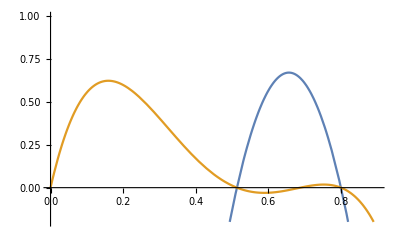

```mathematica
Plot[{((f[f[x]]-x)/x)/(x-(1-1/r))/.r->3.2,(f[f[x]]-x)/.r->3.2},{x,0,1},PlotRange->{{0,0.9},{-.2,1}}]
```

## Class 20 Universal Aspects of Period Doubling 7/5/2020

Super tracks from hmwk 10.3.13

```mathematica
f[x_]:=r x (1-x)
```

Most values will end up being near the 0.75 as seen in the histogram

```mathematica
f[1/2]/.r->3
```

3/4

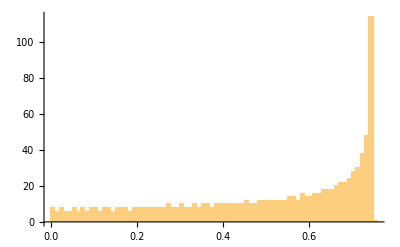

```mathematica
Histogram[Table[f[x]/.r->3,{x,0,1,0.001}],{0.01}]
```

```mathematica
Manipulate[ListPlot[Evaluate[Table[{r,Nest[f,n,k]},{k,1,5},{r,3,4,0.01}]],Joined->True,PlotRange->{{3,4},{0,1}}],{n,1/2,1,0.01}]
```

```mathematica
TraditionalForm@D[f[x],x]
```

r (1-x)-r x

```mathematica
Manipulate[Plot[r (1-x)-r x,{x,0,.75},PlotLabel->"Derivative when x=1/2 is 0"],{r,1,4}]
```

```mathematica
Nest[f,1/2,3]
```

1/4 (1-r/4) r^3 (1-1/4 (1-r/4) r^2)

```mathematica
Expand[1/4 (1-r/4) r^3 (1-1/4 (1-r/4) r^2)]
```

```mathematica
r^3/4-r^4/16-r^5/16+r^6/32-r^7/256-(1-1/r)
```

```mathematica
Solve[-1+1/r+r^3/4-r^4/16-r^5/16+r^6/32-r^7/256==0&&r>=3,r]
```

{{r→Root3.68Root[-8-4 #1-2 #1^2+#1^3&,1]3.6785735104283224}}

```mathematica
N[{{r->Root[-8-4 #1-2 #1^2+#1^3&,1,0]}}]
```

{{r→3.67857}}

## Class 21 Renormalization and Feigenbaum Analysis

Exercise 10.7 .2 - renormalization using the scalar values (R0=2,R1=3.23)

```mathematica
f[x_]:=r x(1-x);
```

```mathematica
f[x,Subscript[r, 0]]/.Subscript[r, 0]->2.0
```

2. (1-x) x

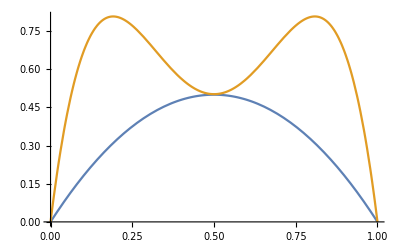

```mathematica
Plot[{f[x]/.r->2,f[f[x]]/.r->3.23},{x,0,1}]
```

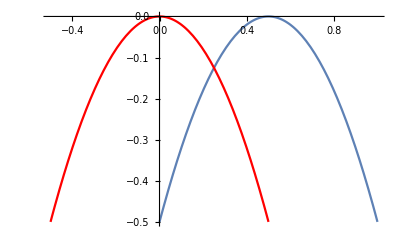

```mathematica
Show[Plot[{(f[x]-0.5)/.r->2},{x,0,1}],Graphics[Translate[Plot[{(f[x])/.r->2},{x,0,1},PlotStyle->Red][[1]],{-0.5,-0.5}]],PlotRange->All]
```

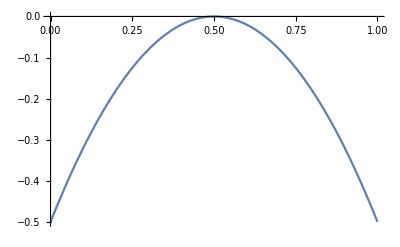

```mathematica
Plot[{(f[x]-0.5)/.r->2},{x,0,1}]
```

Playing with a plot of the scaled variant vs the original, see the scaled version with α set to 2.5.

```mathematica
Manipulate[Plot[{r^2 x-r^2 x^2-r^3 x^2+2 r^3 x^3-r^3 x^4,r^2 x-(r^3 x^4)/α^3+(2 r^3 x^3)/α^2-(r^2 x^2)/α-(r^3 x^2)/α},{x,0,1}],{r,3,4,0.01},{α,2.5,2.5}]
```

Note the first term in both are equal, otherwise each term is a scaled by α

```mathematica
f[x_,n_]:=Subscript[x, n]
```

```mathematica
f[f[x,1],2]/.x->α Subscript[y, n]
```

((α y_n)_1)_2

```mathematica
f[f[x/α,1],2]*α/.x->α Subscript[y, n]
```

α y_n_1_2

## Class 22 Renormalization and Period Doubling

Notes in rocketbook

Algebraic argument for δ

Solve for the points p and q

```mathematica
Solve[{p==-(1+μ)q+q^2,q==-(1+μ)p+p^2},{p,q}]
```

{{p→0,q→0},{p→2+μ,q→2+μ},{p→1/2 (μ-√μ √(4+μ)),q→1/2 (μ+√μ √(4+μ))},{p→1/2 (μ+√μ √(4+μ)),q→1/2 (μ-√μ √(4+μ))}}

More algebra derivation in small notebook

## Class 23 Fractals and the geometry of strange attractors 7/13/2020

Folding and stretching of dough as an analogy of why Chaos occurs.

Rossler Attractor

```mathematica
ParametricPlot3D[{-y-z,x+0.2 y,0.2+z(x-5.7)},{x,-5,5},{y,-5,5},{z,-5,5}(*,VectorPoints->8,VectorSizes->.45*)]
```

```mathematica
f={X,Y,Z}/.NDSolve[{
X'[t]==-(Y[t]+Z[t]),
Y'[t]==X[t]+0.2 Y[t],
Z'[t]==0.2+X[t]Z[t]-5.2 Z[t],
X[0]==1,Y[0]==1,Z[0]==1},
{X,Y,Z},{t,0,300}][[1]];
```

```mathematica
ParametricPlot3D[#[t]&/@f,{t,0,300},BoxRatios->{1,1,1},PlotRange->All,PlotPoints->1500]
```

## Class 24 Henon Map

Jacobian calculation to show the map contracts area (based off multivariable calculus of the determinant of the Jacobian)

```mathematica
Hyperlink["https://www.khanacademy.org/math/multivariable-calculus/multivariable-derivatives/jacobian/v/the-jacobian-determinant"]
```

https://www.khanacademy.org/math/multivariable-calculus/multivariable-derivatives/jacobian/v/the-jacobian-determinant

```mathematica
jacob=D[{Subscript[y, n]+1-a Subscript[x, n]^2,b Subscript[x, n]},{{Subscript[x, n],Subscript[y, n]}}]
```

{{-2 a x_n,1},{b,0}}

```mathematica
jacob//TraditionalForm
```

(-2 a x_n | 1
b | 0)

```mathematica
Det[jacob]
```

-b

## Class 25 Use Chaos to send messages